### a)

```mathematica
Clear["Global`*"]
r[r_]=μ*r-r^3;
θ[r_]=ω+ν*r^2;

s = Solve[r[r]==0,{r}]
```

{{r→0},{r→-√μ},{r→√μ}}

```mathematica
{{r->0},{r->-√μ},{r->√μ}}
p = (Sqrt[μ]*θ[Sqrt[μ]])/(2*π*Sqrt[μ])
```

{{r→0},{r→-√μ},{r→√μ}}

(μ ν+ω)/(2 π)

### b)

```mathematica
X1dot[X1_,X2_]:=1/10*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
X2dot[X1_,X2_]:=X1+1/10*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;
F1:=X1'[t]==1/10*X1[t]-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3;
F2:=X2'[t]==X1[t]+1/10X2[t]+X1[t]*X2[t]+X1[t]^3-X2[t]^3-X1[t]^2*X2[t];
LC =NDSolve[{F1,F2,X1[0]==X2[0]==0.01},{X1,X2},{t,0,100}];
traj = ParametricPlot[
Evaluate[{X1[t],X2[t]}/.{LC},{t,0,100},PlotStyle->{Red}]]/.
Line[x_]->{Arrowheads[{0,0.06,0.06,0}],Arrow[x]},{-0.5,0.5};

plot = StreamPlot[{X1dot[X1,X2], X2dot[X1,X2]},{X1,-1,1},{X2,-1,1},FrameLabel->{"X1","X2"}];
Show[plot,traj]
```

Syntax::tsntxi: "traj=ParametricPlot[Evaluate[{X1[t],X2[t]}/.{LC},{t,0,100},PlotStyle→{Red}]]/.Line[x_]→{Arrowheads[{0,0.06,0.06,0}],Arrow[x]},{-0.5,0.5};" is incomplete; more input is needed.

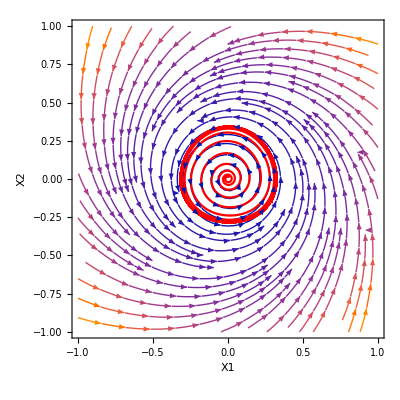

### c)

```mathematica
(*Comparing coefficients one can see that μ=1/10, ω=1, ν=1 makes the systems identical*)
```

### d)

{{1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2,-1-X1[t]^2-2 X1[t] X2[t]-3 X2[t]^2},{1+3 X1[t]^2-2 X1[t] X2[t]+X2[t]^2,1/10-X1[t]^2+2 X1[t] X2[t]-3 X2[t]^2}}

{{1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2,-1-X1[t]^2-2 X1[t] X2[t]-3 X2[t]^2},{1+3 X1[t]^2-2 X1[t] X2[t]+X2[t]^2,1/10-X1[t]^2+2 X1[t] X2[t]-3 X2[t]^2}}

{{1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2,-1-X1[t]^2-2 X1[t] X2[t]-3 X2[t]^2},{1+3 X1[t]^2-2 X1[t] X2[t]+X2[t]^2,1/10-X1[t]^2+2 X1[t] X2[t]-3 X2[t]^2}}

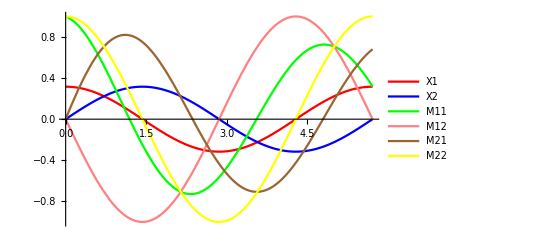

```mathematica
Clear["Global`*"]
μ=1/10;ω=1;ν=1;T= (2 π)/(μ ν+ω);
X1Dot[X1_,X2_]:=1/10*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
X2Dot[X1_,X2_]:=X1+1/10*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;
Dynsys = {X1'[t]==1/10*X1[t]-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,X2'[t]==X1[t]+1/10*X2[t]+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t]};
jacobian = {{D[X1Dot[X1[t],X2[t]],X1[t]],D[X1Dot[X1[t],X2[t]],X2[t]]},{D[X2Dot[X1[t],X2[t]],X1[t]],D[X2Dot[X1[t],X2[t]],X2[t]]}}
{{1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2,-1-X1[t]^2-2 X1[t] X2[t]-3 X2[t]^2},{1+3 X1[t]^2-2 X1[t] X2[t]+X2[t]^2,1/10-X1[t]^2+2 X1[t] X2[t]-3 X2[t]^2}}
r0 = Sqrt[μ];
solution = NDSolve[Join[{Dynsys[[1]],Dynsys[[2]],M11'[t]==jacobian[[1]][[2]]*M21[t]+jacobian[[1]][[1]]*M11[t],M12'[t]==jacobian[[1]][[2]]*M22[t]+ jacobian[[1]][[1]]*M12[t],M21'[t] == jacobian[[2]][[2]]*M21[t]+jacobian[[2]][[1]]*M11[t],M22'[t] == jacobian[[2]][[2]]*M22[t]+jacobian[[2]][[1]]*M12[t],
X1[0]== r0, X2[0]==0, M11[0]==M22[0]==1,M12[0]==M21[0]==0}],{X1, X2, M11, M12, M21, M22},{t,0,T}];
{{1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2,-1-X1[t]^2-2 X1[t] X2[t]-3 X2[t]^2},{1+3 X1[t]^2-2 X1[t] X2[t]+X2[t]^2,1/10-X1[t]^2+2 X1[t] X2[t]-3 X2[t]^2}}
Plot[{X1[t]/. solution, X2[t]/. solution,M11[t]/. solution, M12[t]/. solution,M21[t]/. solution,M22[t]/. solution},{t,0,T}, PlotLegends->{"X1", "X2", "M11", "M12", "M21","M22"},PlotStyle->{Red, Blue, Green, Pink, Brown,Yellow}]
```

### e)

```mathematica
M11 = M11[T]/.solution[[1]];
M12  = M12[T]/.solution[[1]];
M21 = M21[T]/.solution[[1]];
M22 = M22[T]/.solution[[1]];
M = {{M11, M12},{M21, M22}}
```

{{0.319053,2.12317×10^-8},{0.680947,1.}}

### f)

```mathematica
Log[Eigenvalues[M]]/T
```

{5.78753×10^-9,-0.2}

### g,h)

```mathematica
Clear["Global`*"];

(*Define the parameters*)
mu=1/10;
omega=1;
nu=1;

(*Calculate T*)
T=(2 Pi)/(mu*nu+omega);

(*Define the functions r and theta*)
r[rr_]:=mu*rr-rr^3;
theta[rr_]:=omega+nu*rr^2;

(*Define the Jacobian matrix J*)
J[rr_]:=D[{r[rr],theta[rr]},{rr,theta[rr]}];

(*Define the matrix M*)
M[rr_]:=IdentityMatrix[2].MatrixExp[J[rr]*t];

(*Define the derivative matrix der*)
jacpol[X1_,X2_]:=D[{Sqrt[X1^2+X2^2],ArcTan[X1,X2]},{X1,X2}]/. {X1->r[rr]*Cos[theta[rr]],X2->r[rr]*Sin[theta[rr]]};

(*Simplify der and substitute values for r and theta*)
jacpol=Simplify[[X1,X2],Assumptions->rr>0]/. {rr->Sqrt[mu],theta[rr]->0};
dinv[r_] := {{D[r*Cos[θ],r],D[r*Cos[θ],θ]}, {D[r*Sin[θ],r],D[r*Sin[θ],θ]}};
dinv = dinv[r];
cartesian = dinv.M.jacpol ;
cartesian = Simplify[cartesian] /. {r-> Sqrt[μ], θ-> 0, t -> T}
λ = 1/T*Log[Eigenvalues[cartesian] /. r-> Sqrt[μ]]
```

{{ⅇ^(-4 π/11),0},{1-ⅇ^(-4 π/11),1}}

{0,-1/5}